```mathematica
Quit[]
```

This notebook can be used to find the thermal history of the Universe in the Standard Model.

### Basic Instructions

The code works as follows:

1) Evaluate the Basic Modules Section. 
2) Evaluate the Standard Model Section. It takes ~.1d1 s per example evaluation.
3) Evaluate the Standard Model with neutrino chemical potentials Section. It takes ~2 s per example evaluation.

Note that everything is in MeV Units but the rates, the Hubble parameter and time which are in seconds.

### Basic Modules (needs to be loaded first)

This Section loads the main common Modules: 
	1) Constants and Parameters 
	2) Finite Temperature QED corrections 
	3) Thermodynamic Formulae 
	4) SM ν-ν and ν-e Interaction Rates
	
These modules are loaded from BasicModules_v2.m. One can alternatively copy the content of BasicModules_v2.nb here and load it locally.

#### Initialization options

```mathematica
orderQED=3; 
 (* 
QED corrections are coded up to O(e^5), the default is 3 without momentum dependent contributions at O(e^2);
orderQED=2 : O(e^2);
orderQED=3 : O(e^3);
orderQED=4 : O(e^4);
orderQED=5 : O(e^5);
orderQED=6 : O(e^5) + momentum dependent piece at  O(e^2); Else, the QED corrections will be set to 0
*)

 (* If you are not modifying the value of the electron mass or the value of α we strongly recommend simply loading the file *)
flagQED="FILE";
 (* Default and recommended: "FILE" ; -- If you are not modifying the value of me or α it is highly recommended;
            other options : "BESSEL" (using Bessel functions, orderQED=6 does not work).;
                                      If chosen you can also play with the order: nBesselmaxQED = 30.
                        : "FULL"   (not recommended, as it uses numerical integration which is extremely costly) *)
flagthermo="BESSEL"; 
nBesselmaxBSM=30;  
(* Default and recommended: "BESSEL" (this is highly recommended as it speeds up the calculaion by a factor of 10);
									 (if chosen, then one can set up the order of Bessel functions nBesselmaxBSM= 30);
              other option: "FULL" (recommended only if μ/T > 0.1 for some reason)  *)
```

#### Load the basic modules

```mathematica
(* Load the module. If you want to input any parameter do it before loading *)
SetDirectory[NotebookDirectory[]];
Quiet[<<BasicModules_source/nudec_v2.m];

Print["Various superflous error messages have been suppressed"]
Off[General::munfl]
Off[NIntegrate::inumr]
```

Various superflous error messages have been suppressed

### Initial conditions

```mathematica
Tmax=10.0000;
Tmin=0.009;
μoverTini=-10^-7 Tmax;
```

### Standard Model [no chemical potentials]

#### Hubble Parameter and total Energy and Pressure of the Universe

```mathematica
Clear[ρtot,ptot,Hubble,RHSec];
ρtot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+2ρFD[Tνe,μνe]+4ρFD[Tνμ,μνμ]-Pint[Tγ]+Tγ dPintdT[Tγ]);
ptot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+2pFD[Tνe,μνe]+4pFD[Tνμ,μνμ]+Pint[Tγ]);
Hubble[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=((ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;
RHSec[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ](ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]+ ptot[Tγ,Tνe,Tνμ,μνe,μνμ]);
```

```mathematica
1/(Tmax^4(2 π^2)/45)(ρtot[Tmax,Tmax,Tmax,0,0]+ptot[Tmax,Tmax,Tmax,0,0])
```

10.7358

#### Temperature ODEs

```mathematica
Clear[dTγdt,dTνdt,dTνedt,dTνμdt];

(* Equation 2.14 of 1812.05605 *)
dTγdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me]+Tγ d2PintdT2[Tγ])( Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( 4 2 ρBE[Tγ,0]+3 4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me])+3 Tγ dPintdT[Tγ]) + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);

(* Equations 2.9 of 1812.05605 *)
dTνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] Tνe +1/3 ((ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])/(2dρFDdT[Tνe,μνe]));

dTνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] Tνe + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]/(2dρFDdT[Tνe,μνe]);
dTνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] Tνμ + ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]/(2dρFDdT[Tνμ,μνμ]);
```

#### Definition of observables

```mathematica
Clear[Nefffunc,gstars,gstar,OmeganuMdiv,heff];

Nefffunc[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=8/7(11/4)^(4/3)(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ])/(2ρBE[Tγ,0]);

gstars[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=45/(2 π^2 Tγ^3)(2 sFD[Tνe,μνe]+4sFD[Tνμ,μνμ]+2sBE[Tγ,0]+4sFDM[Tγ,0,me]);

gstar[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=30/π^2 ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]/Tγ^4;

OmeganuMdiv[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(3/2 rhocrit/Tγ00^3 Tγ^3/(nFD[Tνe,μνe]+2nFD[Tνμ,μνμ]))/.{rhocrit-> 8.0959 10^-11 eV^4,Tγ00-> 2.7255 Kel}/.{Kel->1/11604.51812 eV}/.eV-> 1;

heff[aTγfinal_]:=1/(Tmax^4(2 π^2)/45)(ρtot[Tmax,Tmax,Tmax,0,0]+ptot[Tmax,Tmax,Tmax,0,0])*(1/aTγfinal)^3;
```

#### SM Key Functions

```mathematica
(* Function used to solve for neutrino decoupling considering a common neutrino temperature.*)
(* Otputs: Tγ[t], Tν[t], t0, tmax *)
FuncSMnudec[]:=(

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);
tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tν[t],Tν[t],0,0],
Tν'[t]==dTνdt[Tγ[t],Tν[t],Tν[t],0,0],aTν'[t]==aTν[t]/Tν[t](dTνdt[Tγ[t],Tν[t],Tν[t],0,0]+Tν[t]Hubble[Tγ[t],Tν[t],Tν[t],0,0]),aTγ'[t]==aTγ[t]/Tγ[t](dTγdt[Tγ[t],Tν[t],Tν[t],0,0]+Tγ[t]Hubble[Tγ[t],Tν[t],Tν[t],0,0]),
Tγ[t0]==Tmax,Tν[t0]==Tmax,aTν[t0]==1,aTγ[t0]==1},{Tγ,Tν,aTν,aTγ},{t,t0,tmax},PrecisionGoal->9,AccuracyGoal->9];

tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

ClearAll[Tγoftfunc,Tνoftfunc,aTνfunc,aTγfunc];
Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνoftfunc[t1_]:=(Tν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTνfunc[t1_]:=(aTν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTγfunc[t1_]:=(aTγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

tvec=Table[10^i,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])/400}];

Totvec=Table[0,{i,1,Length[tvec]},{j,1,8}];
For[i=1,i≤Length[tvec],i++,
time=tvec[[i]];
Tγtime=Tγoftfunc[time];
Totvec[[i,1]]=time;
Totvec[[i,2]]=Tγoftfunc[time];
Totvec[[i,3]]=Tγtime/Tνoftfunc[time];
Totvec[[i,4]]=Tγtime/Tνoftfunc[time];
Totvec[[i,5]]=0/Tγtime;
Totvec[[i,6]]=0/Tγtime;
Totvec[[i,7]]=aTνfunc[time];
Totvec[[i,8]]=aTνfunc[time];
 ];

filenameval="SM_Results/"<> "SM_Tnucommon"<>".dat";
Totvec[[All,All]]=SetPrecision[Totvec[[All,All]],7];
Print["Thermodynamics are output to: "<> filenameval];
Export[filenameval,Totvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"#time (s)" ,"Tγ [MeV]   ",        "Tγ/Tνe     ",        "Tγ/Tνmu     ",           "μνe/Tγ       ","μνmu/Tγ       ","a Tνe       ","a Tνμ       "}];

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ,ρtotoft,ptotoft,Hubbleoft,Totvec];


{Tγoftfunc[t],Tνoftfunc[t],t0,tmax});


(* Function used to solve for neutrino decoupling considering Tνe ≠ Tνμ. *)
(* Otputs: Tγ[t], Tνe[t], Tνμ[t], t0, tmax *)
FuncSMnudecflav[]:=(

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);
tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tνe[t],Tνμ[t],0,0],
Tνe'[t]==dTνedt[Tγ[t],Tνe[t],Tνμ[t],0,0],Tνμ'[t]==dTνμdt[Tγ[t],Tνe[t],Tνμ[t],0,0],aTνe'[t]==aTνe[t]/Tνe[t](dTνedt[Tγ[t],Tνe[t],Tνμ[t],0,0]+Tνe[t]Hubble[Tγ[t],Tνe[t],Tνμ[t],0,0]),aTνμ'[t]==aTνμ[t]/Tνμ[t](dTνμdt[Tγ[t],Tνe[t],Tνμ[t],0,0]+Tνμ[t]Hubble[Tγ[t],Tνe[t],Tνμ[t],0,0]),aTγ'[t]==aTγ[t]/Tγ[t](dTγdt[Tγ[t],Tνe[t],Tνμ[t],0,0]+Tγ[t]Hubble[Tγ[t],Tνe[t],Tνμ[t],0,0]),
Tγ[t0]==Tmax,Tνe[t0]==Tmax,Tνμ[t0]==Tmax,aTνe[t0]==1,aTνμ[t0]==1,aTγ[t0]==1},{Tγ,Tνe,Tνμ,aTνe,aTνμ,aTγ},{t,t0,tmax},PrecisionGoal->9,AccuracyGoal->9];

tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνeoftfunc[t1_]:=(Tνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνμoftfunc[t1_]:=(Tνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTνefunc[t1_]:=(aTνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTνμfunc[t1_]:=(aTνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTγfunc[t1_]:=(aTγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

tvec=Table[10^i,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])/400}];

Totvec=Table[0,{i,1,Length[tvec]},{j,1,8}];
For[i=1,i≤Length[tvec],i++,
time=tvec[[i]];
Tγtime=Tγoftfunc[time];
Totvec[[i,1]]=time;
Totvec[[i,2]]=Tγoftfunc[time];
Totvec[[i,3]]=Tγtime/Tνeoftfunc[time];
Totvec[[i,4]]=Tγtime/Tνμoftfunc[time];
Totvec[[i,5]]=0/Tγtime;
Totvec[[i,6]]=0/Tγtime;
Totvec[[i,7]]=aTνefunc[time];
Totvec[[i,8]]=aTνμfunc[time];
 ];

filenameval="SM_Results/"<> "SM_TnueTnumu"<>".dat";
Totvec[[All,All]]=SetPrecision[Totvec[[All,All]],7];
Print["Thermodynamics are output to: "<> filenameval];
Export[filenameval,Totvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"#time (s)" ,"Tγ [MeV]   ",        "Tγ/Tνe     ",        "Tγ/Tνmu     ",           "μνe/Tγ       ","μνmu/Tγ       ","a Tνe       ","a Tνμ       "}];

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ,ρtotoft,ptotoft,Hubbleoft,Totvec];

{Tγoftfunc[t],Tνeoftfunc[t],Tνμoftfunc[t],t0,tmax});
```

#### SM Examples for the two cases considered:

Case with all temperatures equal and no chemical potentials

tCPU = 2.5058

Thermodynamics are output to: SM_Results/SM_Tnucommon.dat

N_eff     = 3.04528

g_*      = 3.3832

g_(*s)      = 3.9307

h_eff      = 3.9305

∑m_ν/Ω_ν  = 93.013 eV

T_γ/T_νe   = 1.3957823

T_γ/T_νμ   = 1.3957823

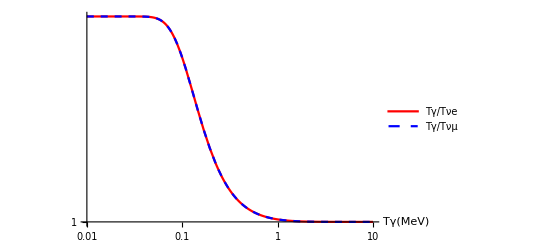

```mathematica
Print["Case with all temperatures equal and no chemical potentials"]
resvec=Quiet[FuncSMnudec[]];

Clear[Tγoft,Tνoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνoft[tt_]:=resvec[[2]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνofTγ[Tgam_]:=Tgam/Tνoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],0,0];
Tratio=Tγoft[tmax]/Tνoft[tmax];

Print["N_eff     = ", NumberForm[Neffval,6]];
Print["g_*      = ", NumberForm[gstarval,5]];
Print["g_(*s)      = ", NumberForm[gstarsval,5]];
Print["h_eff      = ", NumberForm[heff[aTγfunc[tmax]],5]];
Print["∑m_ν/Ω_ν  = ",NumberForm[omeganuval,5] , " eV"];
Print["T_γ/T_νe   = ", NumberForm[Tratio,8]];
Print["T_γ/T_νμ   = ", NumberForm[Tratio,8]];

LogLogPlot[{TγdTνofTγ[Tgam],TγdTνofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

Case with Tnue different than Tnumu and no chemical potentials

tCPU = 2.61688

Thermodynamics are output to: SM_Results/SM_TnueTnumu.dat

N_eff     = 3.0443

g_*      = 3.3828

g_(*s)      = 3.9302

h_eff      = 3.9301

∑m_ν/Ω_ν  = 93.035 eV

T_γ/T_νe   = 1.3945995

T_γ/T_νμ   = 1.3965375

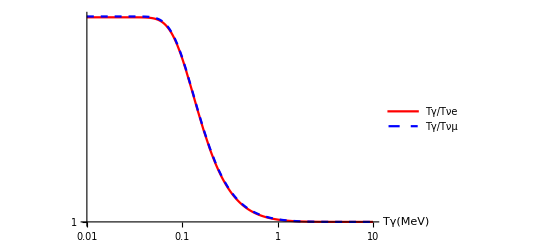

```mathematica
Print["Case with Tnue different than Tnumu and no chemical potentials"]
resvec=Quiet[FuncSMnudecflav[]];

Clear[Tγoft,Tνoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνeoft[tt_]:=resvec[[2]]/.{t-> tt};
Tνmuoft[tt_]:=resvec[[3]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];


Neffval=Nefffunc[Tγoft[tmax],Tνeoft[tmax],Tνmuoft[tmax],0,0];
gstarval=gstar[Tγoft[tmax],Tνeoft[tmax],Tνmuoft[tmax],0,0];
gstarsval=gstars[Tγoft[tmax],Tνeoft[tmax],Tνmuoft[tmax],0,0];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνeoft[tmax],Tνmuoft[tmax],0,0];


Print["N_eff     = ", NumberForm[Neffval,5]];
Print["g_*      = ", NumberForm[gstarval,5]];
Print["g_(*s)      = ", NumberForm[gstarsval,5]];
Print["h_eff      = ", NumberForm[heff[aTγfunc[tmax]],5]];
Print["∑m_ν/Ω_ν  = ",NumberForm[omeganuval,5] , " eV"];
Print["T_γ/T_νe   = ", NumberForm[Tγoft[tmax]/Tνeoft[tmax],8]];
Print["T_γ/T_νμ   = ", NumberForm[Tγoft[tmax]/Tνmuoft[tmax],8]];

LogLogPlot[{Tgam/Tνeoft[tofTγ[Tgam]],Tgam/Tνmuoft[tofTγ[Tgam]]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

#### Check on the continuity equation

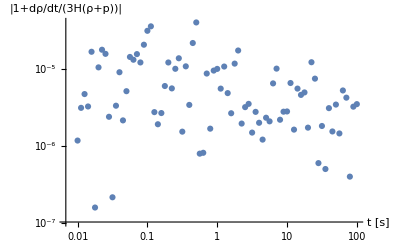

```mathematica
ListLogLogPlot[Table[{10^tval,Abs[1-D[ρtot[Tγ[t],Tνe[t],Tνμ[t],0,0],t]/RHSec[Tγ[t],Tνe[t],Tνμ[t],0,0]/.First[solEarlyUniverset]]/.t->10^tval},{tval,-2,2,0.05}],AxesLabel->{"t [s]","|1+dρ/dt/(3H(ρ+p))|"}]
```

### Standard Model [with neutrino chemical potentials]

#### Hubble Parameter and total Energy and Pressure of the Universe

```mathematica
Clear[ρtot,ptot,Hubble,RHSec];
ρtot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+2ρFD[Tνe,μνe]+4ρFD[Tνμ,μνμ]-Pint[Tγ]+Tγ dPintdT[Tγ]);
ptot[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+2pFD[Tνe,μνe]+4pFD[Tνμ,μνμ]+Pint[Tγ]);
Hubble[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=((ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;
RHSec[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ](ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]+ ptot[Tγ,Tνe,Tνμ,μνe,μνμ]);
```

#### Temperature ODEs

```mathematica
Clear[dTγdt,dTνdt,dTνedt,dTνμdt,dμνdt,dμνedt,dμνμdt];

(* Equation 3.2 of 2001.04466 *)
dTγdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me]+Tγ d2PintdT2[Tγ])( Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( 4 2 ρBE[Tγ,0]+3 4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me])+3 Tγ dPintdT[Tγ]) + ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);


(* Equation 2.9a of 2001.04466 *)
dTνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( (ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdμ[Tνe,μνe]-nFD[Tνe,μνe]dρFDdμ[Tνe,μνe]) +dnFDdμ[Tνe,μνe] 1/2 ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]-dρFDdμ[Tνe,μνe] 1/2 ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]);

dTνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=1/(dnFDdμ[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]-dnFDdT[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( (ρFD[Tνμ,μνμ]+pFD[Tνμ,μνμ])dnFDdμ[Tνμ,μνμ]-nFD[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ]) +dnFDdμ[Tνμ,μνμ] 1/2 ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]-dρFDdμ[Tνμ,μνμ] 1/2 ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]);

dTνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ( (ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdμ[Tνe,μνe]-nFD[Tνe,μνe]dρFDdμ[Tνe,μνe]) +dnFDdμ[Tνe,μνe] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdμ[Tνe,μνe] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

(*The factor of 1/2 accounts for the fact that we are considering a single neutrino species, not the neutrino + antineutrino *)

(* Equation 2.9b of 2001.04466 *)
dμνdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdT[Tνe,μνe]-nFD[Tνe,μνe]dρFDdT[Tνe,μνe]) +dnFDdT[Tνe,μνe] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdT[Tνe,μνe] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

dμνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdT[Tνe,μνe]-nFD[Tνe,μνe]dρFDdT[Tνe,μνe]) +dnFDdT[Tνe,μνe] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdT[Tνe,μνe] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

dμνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]-dnFDdT[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνμ,μνμ]+pFD[Tνμ,μνμ])dnFDdT[Tνμ,μνμ]-nFD[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]) +dnFDdT[Tνμ,μνμ] 1/2(1/3(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]))-dρFDdT[Tνμ,μνμ] 1/2(1/3(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]+2ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])));

dμνedt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνe,μνe]dρFDdT[Tνe,μνe]-dnFDdT[Tνe,μνe]dρFDdμ[Tνe,μνe])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνe,μνe]+pFD[Tνe,μνe])dnFDdT[Tνe,μνe]-nFD[Tνe,μνe]dρFDdT[Tνe,μνe]) +dnFDdT[Tνe,μνe] 1/2(ΔρSMνe[Tγ,Tνe,Tνμ,μνe,μνμ])-dρFDdT[Tνe,μνe] 1/2(ΔnSMνe[Tγ,Tνe,Tνμ,μνe,μνμ]));

dμνμdt[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=-1/(dnFDdμ[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]-dnFDdT[Tνμ,μνμ]dρFDdμ[Tνμ,μνμ])(- 3 Hubble[Tγ,Tνe,Tνμ,μνe,μνμ] ((ρFD[Tνμ,μνμ]+pFD[Tνμ,μνμ])dnFDdT[Tνμ,μνμ]-nFD[Tνμ,μνμ]dρFDdT[Tνμ,μνμ]) +dnFDdT[Tνμ,μνμ] 1/2(ΔρSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ])-dρFDdT[Tνμ,μνμ] 1/2(ΔnSMνμ[Tγ,Tνe,Tνμ,μνe,μνμ]));
```

#### Definition of observables

```mathematica
Clear[Nefffunc,gstars,gstar,OmeganuMdiv,heff];

Nefffunc[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=8/7(11/4)^(4/3)(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ])/(2ρBE[Tγ,0]);

gstars[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=45/(2 π^2 Tγ^3)(2 sFD[Tνe,μνe]+4sFD[Tνμ,μνμ]+2sBE[Tγ,0]+4sFDM[Tγ,0,me]);

gstar[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=30/π^2 ρtot[Tγ,Tνe,Tνμ,μνe,μνμ]/Tγ^4;

OmeganuMdiv[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(3/2 rhocrit/Tγ00^3 Tγ^3/(nFD[Tνe,μνe]+2nFD[Tνμ,μνμ]))/.{rhocrit-> 8.0959 10^-11 eV^4,Tγ00-> 2.7255 Kel}/.{Kel->1/11604.51812 eV}/.eV-> 1;

heff[aTγfinal_]:=(ρtot[Tmax,Tmax,Tmax,0,0]+ptot[Tmax,Tmax,Tmax,0,0])/(Tmax^4(2 π^2)/45)*(1/aTγfinal)^3;
```

#### SM with chemical potentials: Key Functions

```mathematica
(* Function used to solve for neutrino decoupling considering a common Tν and μν .*)
(* Otputs: Tγ[t], Tν[t], μν[t], t0, tmax *)
FuncSMnudecchem[]:=(

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);
tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]],
Tν'[t]==dTνdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]],
μν'[t]==dμνdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]],aTν'[t]==aTν[t]/Tν[t](dTνdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]]+Tν[t]Hubble[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]]),
aTγ'[t]==aTγ[t]/Tγ[t](dTγdt[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]]+Tγ[t]Hubble[Tγ[t],Tν[t],Tν[t],μν[t],μν[t]]),
Tγ[t0]==Tmax,Tν[t0]==Tmax,μν[t0]== μoverTini,aTν[t0]==1,aTγ[t0]==1},{Tγ,Tν,μν,aTν,aTγ},{t,t0,tmax},PrecisionGoal->9,AccuracyGoal->9];
tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνoftfunc[t1_]:=(Tν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
μνoftfunc[t1_]:=(μν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTνfunc[t1_]:=(aTν[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTγfunc[t1_]:=(aTγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

tvec=Table[10^i,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])/400}];

Totvec=Table[0,{i,1,Length[tvec]},{j,1,8}];
For[i=1,i≤Length[tvec],i++,
time=tvec[[i]];
Tγtime=Tγoftfunc[time];
Totvec[[i,1]]=time;
Totvec[[i,2]]=Tγoftfunc[time];
Totvec[[i,3]]=Tγtime/Tνoftfunc[time];
Totvec[[i,4]]=Tγtime/Tνoftfunc[time];
Totvec[[i,5]]=μνoftfunc[time]/Tγtime;
Totvec[[i,6]]=μνoftfunc[time]/Tγtime;
Totvec[[i,7]]=aTνfunc[time];
Totvec[[i,8]]=aTνfunc[time];
 ];

filenameval="SM_Results/"<> "SM_Tnuandmunu"<>".dat";
Totvec[[All,All]]=SetPrecision[Totvec[[All,All]],7];
Print["Thermodynamics are output to: "<> filenameval];
Export[filenameval,Totvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"#time (s)" ,"Tγ [MeV]   ",        "Tγ/Tνe     ",        "Tγ/Tνmu     ",           "μνe/Tγ       ","μνmu/Tγ       ","a Tνe       ","a Tνμ       "}];

{Tγoftfunc[t],Tνoftfunc[t],μνoftfunc[t],t0,tmax});


(* Function used to solve for neutrino decoupling considering Tνe, Tνμ, μνe, μνμ .*)
(* Otputs: Tγ[t], Tνe[t], Tνμ[t], μνe[t], μνμ[t], t0, tmax *)
FuncSMnudecflavchem[]:=(

t0=1/(2 Hubble[Tmax,Tmax,Tmax,0,0]);
tmax=1/(2 Hubble[Tmin,Tmin/1.4,Tmin/1.4,0,0]);

tCPU1=TimeUsed[];
(* Solve the ODE system *)
solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],
Tνe'[t]==dTνedt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],Tνμ'[t]==dTνμdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],
μνe'[t]==dμνedt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],μνμ'[t]==dμνμdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],aTνe'[t]==aTνe[t]/Tνe[t](dTνedt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]+Tνe[t]Hubble[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]),aTνμ'[t]==aTνμ[t]/Tνμ[t](dTνμdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]+Tνμ[t]Hubble[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]),
aTγ'[t]==aTγ[t]/Tγ[t](dTγdt[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]+Tγ[t]Hubble[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]),
Tγ[t0]==Tmax,Tνe[t0]==Tmax,Tνμ[t0]==Tmax,μνe[t0]==μoverTini,μνμ[t0]==μoverTini,aTνe[t0]==1,aTνμ[t0]==1,aTγ[t0]==1},{Tγ,Tνe,Tνμ,μνe,μνμ,aTνe,aTνμ,aTγ},{t,t0,tmax},PrecisionGoal->9,AccuracyGoal->9];
tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνeoftfunc[t1_]:=(Tνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
Tνμoftfunc[t1_]:=(Tνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
μνeoftfunc[t1_]:=(μνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
μνμoftfunc[t1_]:=(μνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTνefunc[t1_]:=(aTνe[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTνμfunc[t1_]:=(aTνμ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};
aTγfunc[t1_]:=(aTγ[t]/.solEarlyUniverset)[[1]]/.{t-> t1};

tvec=Table[10^i,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])/400}];

Totvec=Table[0,{i,1,Length[tvec]},{j,1,8}];
For[i=1,i≤Length[tvec],i++,
time=tvec[[i]];
Tγtime=Tγoftfunc[time];
Totvec[[i,1]]=time;
Totvec[[i,2]]=Tγoftfunc[time];
Totvec[[i,3]]=Tγtime/Tνeoftfunc[time];
Totvec[[i,4]]=Tγtime/Tνμoftfunc[time];
Totvec[[i,5]]=μνeoftfunc[time]/Tγtime;
Totvec[[i,6]]=μνμoftfunc[time]/Tγtime;
Totvec[[i,7]]=aTνefunc[time];
Totvec[[i,8]]=aTνμfunc[time];
 ];

filenameval="SM_Results/"<> "SM_Tnuandmunu_flavor"<>".dat";
Totvec[[All,All]]=SetPrecision[Totvec[[All,All]],7];
Print["Thermodynamics are output to: "<> filenameval];
Export[filenameval,Totvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"#time (s)" ,"Tγ [MeV]   ",        "Tγ/Tνe     ",        "Tγ/Tνmu     ",           "μνe/Tγ       ","μνmu/Tγ       ","a Tνe       ","a Tνμ       "}];


{Tγoftfunc[t],Tνeoftfunc[t],Tνμoftfunc[t],μνeoftfunc[t],μνμoftfunc[t],t0,tmax});
```

#### SM Example Tνe = Tνμ = Tν, μνe = μνμ = μν

```mathematica
resvec=Quiet[FuncSMnudecchem[]];
```

tCPU = 1.14813

Thermodynamics are output to: SM_Results/SM_Tnuandmunu.dat

N_eff     = 3.0445

g_*      = 3.3828

g_(*s)      = 3.9303

h_eff      = 3.9302

∑m_ν/Ω_ν  = 93.109 eV

T_γ/T_νe   = 1.394453

T_γ/T_νμ   = 1.394453

T_νe/μ_νe  = -234.7

T_νμ/μ_νμ  = -234.7

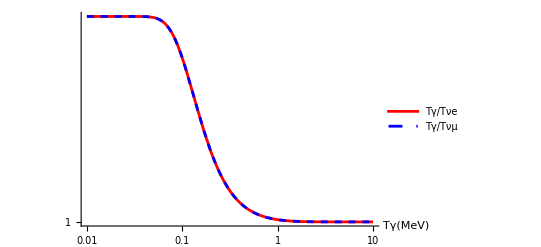

```mathematica
Clear[Tγoft,Tνoft,tofTγ,TγdTνofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνoft[tt_]:=resvec[[2]]/.{t-> tt};
μνoft[tt_]:=resvec[[3]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνofTγ[Tgam_]:=Tgam/Tνoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
Tratio=Tγoft[tmax]/Tνoft[tmax];
μratio=Tνoft[tmax]/μνoft[tmax];

Print["N_eff     = ", NumberForm[Neffval,5]];
Print["g_*      = ", NumberForm[gstarval,5]];
Print["g_(*s)      = ", NumberForm[gstarsval,5]];
Print["h_eff      = ", NumberForm[heff[aTγfunc[tmax]],5]];
Print["∑m_ν/Ω_ν  = ",NumberForm[omeganuval,5] , " eV"];
Print["T_γ/T_νe   = ", NumberForm[Tratio,7]];
Print["T_γ/T_νμ   = ",NumberForm[Tratio,7] ];
Print["T_νe/μ_νe  = ", NumberForm[μratio,4]];
Print["T_νμ/μ_νμ  = ", NumberForm[μratio,4]];

LogLogPlot[{TγdTνofTγ[Tgam],TγdTνofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

#### SM Example Tνe != Tνμ , μνe != μνμ

```mathematica
resvec=Quiet[FuncSMnudecflavchem[]];
```

tCPU = 1.93984

Thermodynamics are output to: SM_Results/SM_Tnuandmunu_flavor.dat

N_eff     = 3.0436

g_*      = 3.3824

g_(*s)      = 3.9299

h_eff      = 3.9297

∑m_ν/Ω_ν  = 93.1282 eV

T_γ/T_νe   = 1.392546

T_γ/T_νμ   = 1.395632

T_νe/μ_νe  = -152.6

T_νμ/μ_νμ  = -341.6

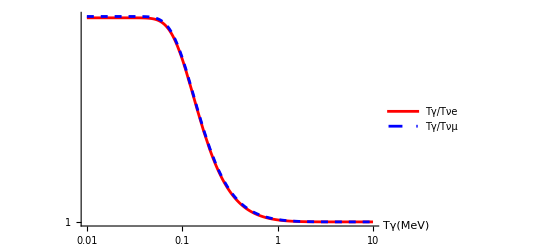

```mathematica
Clear[Tγoft,Tνeoft,Tνμoft,μνeoft,μνμoft,tofTγ,TγdTνeofTγ,TγdTνμofTγ];
Tγoft[tt_]:=resvec[[1]]/.{t-> tt};
Tνeoft[tt_]:=resvec[[2]]/.{t-> tt};
Tνμoft[tt_]:=resvec[[3]]/.{t-> tt};
μνeoft[tt_]:=resvec[[4]]/.{t-> tt};
μνμoft[tt_]:=resvec[[5]]/.{t-> tt};
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];
TγdTνeofTγ[Tgam_]:=Tgam/Tνeoft[tofTγ[Tgam]];
TγdTνμofTγ[Tgam_]:=Tgam/Tνμoft[tofTγ[Tgam]];

Neffval=Nefffunc[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνeoft[tmax],Tνμoft[tmax],μνeoft[tmax],μνμoft[tmax]];
Tratioe=Tγoft[tmax]/Tνeoft[tmax];
Tratioμ=Tγoft[tmax]/Tνμoft[tmax];
μratioe=Tνeoft[tmax]/μνeoft[tmax];
μratioμ=Tνμoft[tmax]/μνμoft[tmax];

Print["N_eff     = ", NumberForm[Neffval,5]];
Print["g_*      = ", NumberForm[gstarval,5]];
Print["g_(*s)      = ", NumberForm[gstarsval,5]];
Print["h_eff      = ", NumberForm[heff[aTγfunc[tmax]],5]];
Print["∑m_ν/Ω_ν  = ",NumberForm[omeganuval,6] , " eV"];
Print["T_γ/T_νe   = ", NumberForm[Tratioe,7]];
Print["T_γ/T_νμ   = ",NumberForm[Tratioμ,7] ];
Print["T_νe/μ_νe  = ", NumberForm[μratioe,4]];
Print["T_νμ/μ_νμ  = ", NumberForm[μratioμ,4]];

LogLogPlot[{TγdTνeofTγ[Tgam],TγdTνμofTγ[Tgam]},{Tgam,10,0.01},PlotLegends->{"Tγ/Tνe","Tγ/Tνμ"},AxesLabel->{"Tγ(MeV)"},PlotStyle->{Red,{Blue,Dashed}}]
```

#### Check on the continuity equation

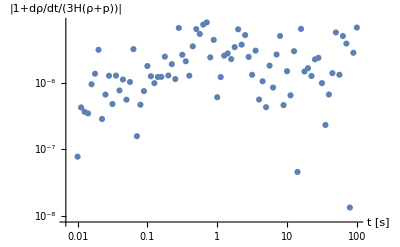

```mathematica
ListLogLogPlot[Table[{10^tval,Abs[1-D[ρtot[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]],t]/RHSec[Tγ[t],Tνe[t],Tνμ[t],μνe[t],μνμ[t]]/.First[solEarlyUniverset]]/.t->10^tval},{tval,-2,2,0.05}],AxesLabel->{"t [s]","|1+dρ/dt/(3H(ρ+p))|"}]
```